## Initialization

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Directory[]
```

/Users/npadmana/myWork/np_sandbox/CLASS

## Power Spectrum conventions

Check to see if we have the correct power spectrum conventions for the primordial power spectrum. (Note that we have files for both synchronous and Newtonian gauges -- we will use the synchronous gauge by default, but the Newtonian gauge will be useful for checks later in this document).

```mathematica
(* Read in the power spectrum and plot it -- do this at z=0 *)
```

```mathematica
pk0 = Import["output/synchronous_z1_pk.dat","Table"]//DeleteCases[#, {"#",___}] & ;
```

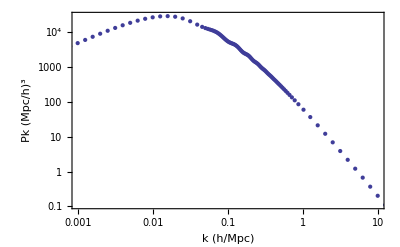

```mathematica
ListLogLogPlot[pk0, PlotRange->{{0.001, 10}, All}, Frame->True, FrameLabel-> {"k (h/Mpc)", "Pk (Mpc/h)^3"}]
```

```mathematica
(* Now read in the transfer functions *)
```

In synchronous gauge, the CDM has no peculiar velocities, so we only need to pull out the baryon velocity transfer function.

```mathematica
(* col 1 is k, col 6 is transfer function for density, col 8 is baryon v transfer fn *)
```

```mathematica
transfer0 = Import["output/synchronous_z1_tk.dat", "Table"]//DeleteCases[#, {"#", ___}] & // Part[#, All, {1,6, 8}] & ;
```

```mathematica
(* Now let us see if we can match the two power spectra, start by defining the primordial P(k) *)

(* pkPrim reads in a k in h/Mpc, but note that it is defined in terms of regular Mpc *)
pkPrim[kh_] := With[{k = kh, ns=0.966, As=2.4*^-9, kpivot=0.002}, As (k/kpivot)^(ns-1)];
```

```mathematica
(* Now scan through the transfer function list and calculate pk *)
```

```mathematica
Clear[pkcalc];pkcalc[kh_, tcdm_, vbary_]:= With[{h=0.703}, {kh, 2 π^2*kh*tcdm^2*pkPrim[kh]/kh^4}];
```

```mathematica
pk0test = pkcalc@@@transfer0;
```

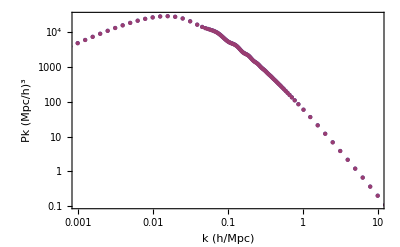

```mathematica
ListLogLogPlot[{pk0, pk0test}, PlotRange->{{0.001, 10}, All}, Frame->True, FrameLabel-> {"k (h/Mpc)", "Pk (Mpc/h)^3"}]
```